# Generation of figures and plots

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\willn\Dev\wsc2019\figures

```mathematica
Grid[Transpose@imageSet[;;5, {Image[#Image, ImageSize->Small], "↓", StringTemplate["`Zoom` km across"][#]}&]//Normal]
Export["fig_examples.png", Rasterize[%, ImageResolution->300]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
↓ | ↓ | ↓ | ↓ | ↓
169.469 km across | 31.6929 km across | 177.526 km across | 89.7375 km across | 58.9002 km across

fig_examples.png

```mathematica
GraphicsRow[{-Graphics-, -Graphics-, -Graphics-,-Graphics-}, 10]
Export["fig_structure.png", Rasterize[%, ImageResolution->300]]
```

-Graphics-

fig_structure.png

```mathematica
Grid[{Image[#, ImageSize->Small]&/@{-Graphics-,-Graphics-,-Graphics-, -Graphics-, -Graphics-,-Graphics-},{"Original", "Binarize[]", "MorphologicalBinarize[]", SpanFromLeft, "ImageForestingComponents[]", SpanFromLeft}}, Spacings->1]
Export["fig_processing.png", Rasterize[%, ImageResolution->300]]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Original | Binarize[] | MorphologicalBinarize[] |  | ImageForestingComponents[] |

fig_processing.png

```mathematica
-Graphics-;
Export["fig_predict.png", ImageResize[%,200]]
```

fig_predict.png

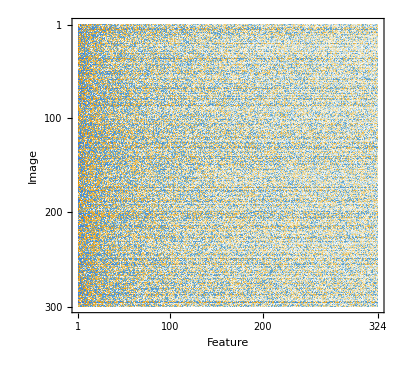
```mathematica
-Graphics-
Export["fig_featurematrix.png", Rasterize[%, ImageResolution->300]]
```

-Graphics-

fig_featurematrix.png

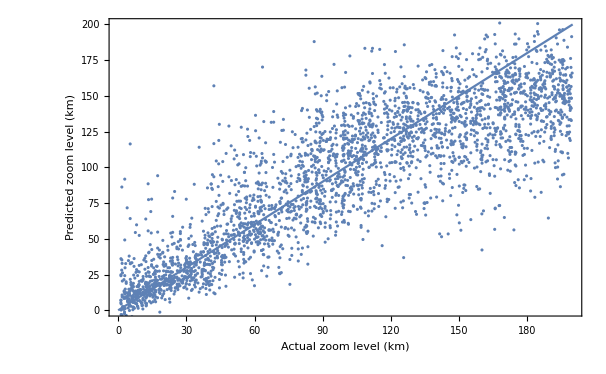
```mathematica
-Graphics-;
Export["fig_resultplot.png", Rasterize[%, ImageResolution->300]]
```

fig_resultplot.png

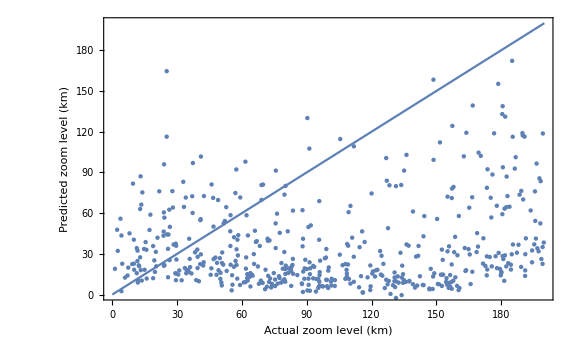
```mathematica
-Graphics-;
Export["fig_resultplotwolfram.png", Rasterize[%, ImageResolution->300]]
```

fig_resultplotwolfram.png

```mathematica
{Image[#, ImageSize->Medium]&/@{-Graphics-,-Graphics-}, {"DigitalGlobe", "Wolfram satellite"}}//Grid
Export["fig_satcomparison.png", Rasterize[%, ImageResolution->300]]
```

-Graphics- | -Graphics-
DigitalGlobe | Wolfram satellite

fig_satcomparison.png

xport[fig_satcomparison.png,-Graphics-]